## Case of two point incident on a parabola

Equation Of Reflective Curve In Parametric and Cartesian Form

```mathematica
curveparaeqn = {8t, -2 t^2+6}
curvecarteqn = Last[List @@ Reduce[Eliminate[{curveparaeqn[[1]]==x,curveparaeqn[[2]]==y}, t],y]]
```

{8 t,6-2 t^2}

1/32 (192-x^2)

Plot of the equation

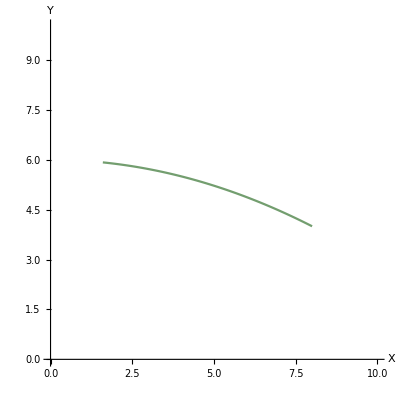

```mathematica
curve = ParametricPlot[curveparaeqn, {t, 0.2, 1},PlotRange->{0, 10},AxesLabel->{"X", "Y"},AxesStyle->Arrowheads[.02], ColorFunction->"BlueGreenYellow"]
```

Incident ray of light at 45 degrees to x axis with source at origin

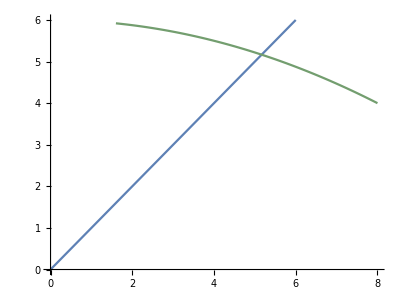

{x→5.16601}

```mathematica
sourceparaeqn = {t, t};
sourcecarteqn = x;
sourceline = ParametricPlot[sourceparaeqn, {t, 0, 6}, PlotRange->All];
Show[sourceline, curve]
a1incipt = N[Solve[sourcecarteqn==curvecarteqn, x]][[2]]
```

Tangent line at point of incident and reflected ray

y==6.83399-0.322876 x

y==-10.834+3.09717 x

m==-6.16601

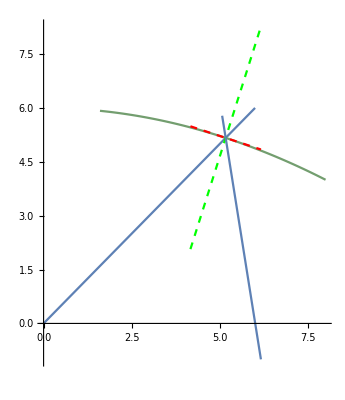

```mathematica
a1taneqn = Reduce[y-(curvecarteqn /. a1incipt)== (D[curvecarteqn, x] /. a1incipt)(x-({x} /.a1incipt)[[1]]),y]
a1noreqn = Reduce[y-(curvecarteqn /. a1incipt)== (-1/(D[curvecarteqn, x] /. a1incipt))(x-({x} /.a1incipt)[[1]]),y]
a1norplot = Plot[Last[List @@ a1noreqn], {x,({x} /.a1incipt)[[1]]-1,({x} /.a1incipt)[[1]]+1}, PlotStyle->Directive[Green, Dashed]];
a1tanplot = Plot[Last[List @@ a1taneqn], {x,({x} /.a1incipt)[[1]]-1,({x} /.a1incipt)[[1]]+1}, PlotStyle->Directive[Red, Dashed]];
a1refangle = Reduce[(1-(-1/(D[curvecarteqn, x] /. a1incipt)))/(1+1*(-1/(D[curvecarteqn, x] /. a1incipt)))== ((-1/(D[curvecarteqn, x] /. a1incipt))-m)/(1+(-1/(D[curvecarteqn, x] /. a1incipt))*m),m]
a1refeqn = Reduce[y-(curvecarteqn /. a1incipt)== Last[List @@ a1refangle](x-({x} /.a1incipt)[[1]]),y];
a1refplot =  Plot[Last[List @@ a1refeqn], {x,({x} /.a1incipt)[[1]]-0.1,({x} /.a1incipt)[[1]]+1}];
Show[sourceline, curve, a1tanplot,a1norplot,a1refplot]
```

Now, on 2nd reflection on the axis

y==-37.0197+6.16601 x

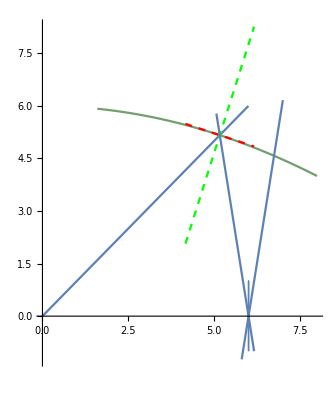

```mathematica
a2incipt = Last[List @@ Reduce[Last[List @@ a1refeqn]==0,x]];
a2noreqn = {a2incipt, y};
a2norplot = ParametricPlot[a2noreqn,{x, -1, 1}, {y, -1, 1}];
a2refangle = (Tan[π]-Last[List @@ a1refangle])/(1+Tan[π]*Last[List @@ a1refangle]);
a2refeqn = Reduce[y-0==a2refangle(x-a2incipt),y]
a2refplot = Plot[Last[List @@ a2refeqn], {x,a2incipt - 0.2,a2incipt+1}];
Show[sourceline, curve, a1tanplot,a1norplot,a1refplot,a2norplot, a2refplot]
```

Now on 3rd Reflection

{x→6.74625}

y==7.42225-0.421641 x

y==-11.4222+2.37169 x

m==1.3508

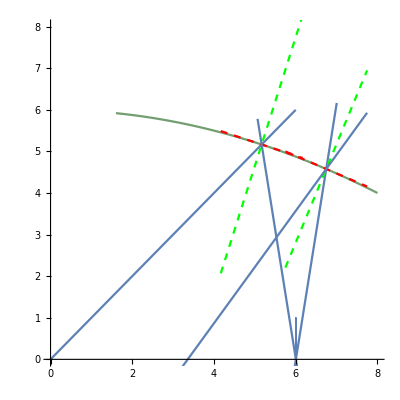

```mathematica
a3incipt = N[Solve[Last[List @@ a2refeqn]==curvecarteqn, x]][[2]]
a3taneqn = Reduce[y-(curvecarteqn /. a3incipt)== (D[curvecarteqn, x] /. a3incipt)(x-({x} /.a3incipt)[[1]]),y]
a3noreqn = Reduce[y-(curvecarteqn /. a3incipt)== (-1/(D[curvecarteqn, x] /. a3incipt))(x-({x} /.a3incipt)[[1]]),y]
a3norplot = Plot[Last[List @@ a3noreqn], {x,({x} /.a3incipt)[[1]]-1,({x} /.a3incipt)[[1]]+1}, PlotStyle->Directive[Green, Dashed]];
a3tanplot = Plot[Last[List @@ a3taneqn], {x,({x} /.a3incipt)[[1]]-1,({x} /.a3incipt)[[1]]+1}, PlotStyle->Directive[Red, Dashed]];
a3refangle = Reduce[(a2refangle-(-1/(D[curvecarteqn, x] /. a3incipt)))/(1+a2refangle*(-1/(D[curvecarteqn, x] /. a3incipt)))== ((-1/(D[curvecarteqn, x] /. a3incipt))-m)/(1+(-1/(D[curvecarteqn, x] /. a3incipt))*m),m]
a3refeqn = Reduce[y-(curvecarteqn /. a3incipt)== Last[List @@ a3refangle](x-({x} /.a3incipt)[[1]]),y];
a3refplot =  Plot[Last[List @@ a3refeqn], {x,({x} /.a3incipt)[[1]]-4,({x} /.a3incipt)[[1]]+1}];
Show[sourceline, curve, a1tanplot,a1norplot,a1refplot,a2norplot, a2refplot, a3tanplot,a3norplot,a3refplot, PlotRange->{{0, 8},{0, 8}}]
```

Plot of points of intersection

{{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0}}

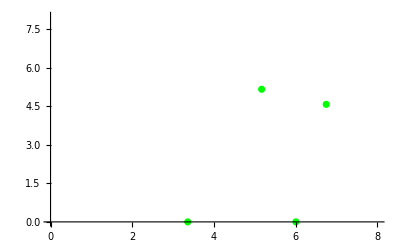

```mathematica
interpts = {{x/.a1incipt,(curvecarteqn /. a1incipt)},{a2incipt, 0},{x /.a3incipt,(curvecarteqn /. a3incipt)},{a4incipt, 0}}
ptplot = ListPlot[interpts, PlotRange->{{0, 8},{0, 8}},PlotStyle->{Green}]
```

Now 4th reflection

y==4.53511-1.3508 x

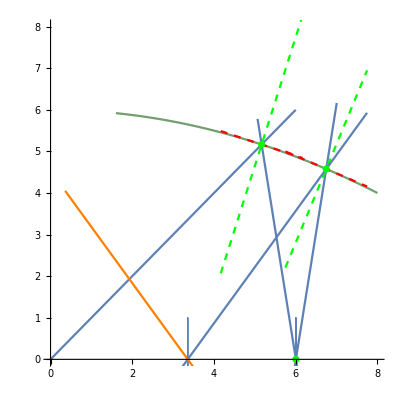

```mathematica
a4incipt = Last[List @@ Reduce[Last[List @@ a3refeqn]==0,x]];
a4noreqn = {a4incipt, y};
a4norplot = ParametricPlot[a4noreqn,{x, -1, 1}, {y, -1, 1}];
a4refangle = (Tan[π]-Last[List @@ a3refangle])/(1+Tan[π]*Last[List @@ a3refangle]);
a4refeqn = Reduce[y-0==a4refangle(x-a4incipt),y]
a4refplot = Plot[Last[List @@ a4refeqn], {x,a4incipt - 3,a4incipt+1}, PlotStyle->Directive[Orange]];
Show[sourceline, curve, a1tanplot,a1norplot,a1refplot,a2norplot, a2refplot, a3tanplot,a3norplot,a3refplot,a4norplot,a4refplot, ptplot, PlotRange->{{0, 8},{0, 8}}]
```

Plot of reflected rays

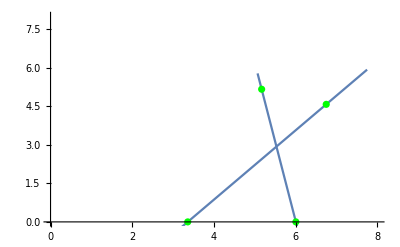

```mathematica
Show[a1refplot,a3refplot,ptplot, PlotRange->{{0, 8},{0, 8}}, AxesOrigin->{0, 0}]
```

Now we have to consider the incident points on the plane mirrors as source if they produce any further reflection. Each point source will lead to a different orthotomic curve. (If the light rays from the sources were parallel we have a relation among them in this case.)

Plotting orthotomic points for each incident point on curve with the respective source

{0,0}

{3.99644,12.3776}

{{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{3.99644,12.3776}}

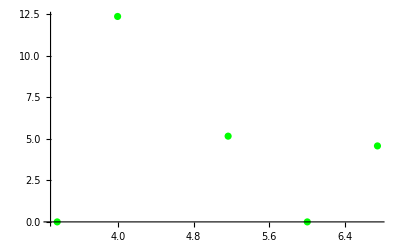

```mathematica
a = 0.322876; b=1; c=-6.83399;
source = {0, 0}
x = (b(b*source[[1]]-a*source[[2]])-a*c)/(a^2+b^2); y=( a(-b*source[[1]]+a*source[[2]])-b*c)/(a^2+b^2);
points = {Last[List @@ Reduce[source[[1]]-x==x-m, m]],Last[List @@ Reduce[source[[2]]-y==y-m, m]]}
AppendTo[interpts, points]
ptplot = ListPlot[interpts, PlotRange->Full,PlotStyle->{Green}]
```

{6.00383,0}

{9.50559,8.30509}

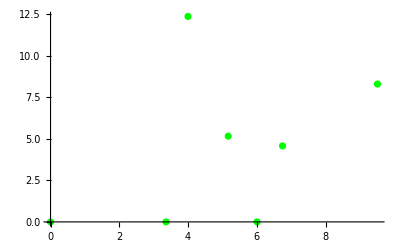

```mathematica
a = 0.4216405353733948; b=1; c=-7.422245928559704;
source = {6.003831069285709,0}
x = (b(b*source[[1]]-a*source[[2]])-a*c)/(a^2+b^2); y=( a(-b*source[[1]]+a*source[[2]])-b*c)/(a^2+b^2);
points2 = {Last[List @@ Reduce[source[[1]]-x==x-m, m]],Last[List @@ Reduce[source[[2]]-y==y-m, m]]}
AppendTo[interpts, points2];
AppendTo[interpts, {0, 0}];
ptplot = ListPlot[interpts, PlotRange->Full,PlotStyle->{Green}]
```

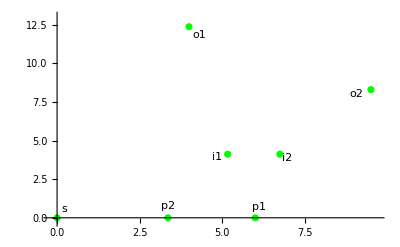

```mathematica
a = 0.4216405353733948; b=1; c=-7.422245928559704;
source = {0,0}
x = (b(b*source[[1]]-a*source[[2]])-a*c)/(a^2+b^2); y=( a(-b*source[[1]]+a*source[[2]])-b*c)/(a^2+b^2);
points3 = {Last[List @@ Reduce[source[[1]]-x==x-m, m]],Last[List @@ Reduce[source[[2]]-y==y-m, m]]}
AppendTo[interpts, points3];
AppendTo[interpts, {0, 0}];
ptplot = ListPlot[interpts, PlotRange->Full,PlotStyle->{Green}]
```

{6.00383,0}

{8.86666,8.86665}

{{5.16601,5.16601},{6.00383,0},{6.74625,4.57775},{3.35734,0},{3.99644,12.3776},{9.50559,8.30509},{0,0},{5.31427,12.6038},{0,0},{8.86666,8.86665}}

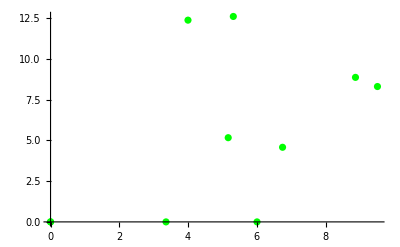

```mathematica
a = 0.322876; b=1; c=-6.83399;
source = {6.003831069285709,0}
x = (b(b*source[[1]]-a*source[[2]])-a*c)/(a^2+b^2); y=( a(-b*source[[1]]+a*source[[2]])-b*c)/(a^2+b^2);
points = {Last[List @@ Reduce[source[[1]]-x==x-m, m]],Last[List @@ Reduce[source[[2]]-y==y-m, m]]}
AppendTo[interpts, points]
ptplot = ListPlot[interpts, PlotRange->Full,PlotStyle->{Green}]
```

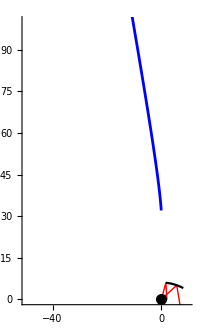

{-(8 t (-32 t^2+8 (-6+2 t^2)))/(64+16 t^2),-(16 (-32 t^2+8 (-6+2 t^2)))/(64+16 t^2)}

{6.00383-(8 t (4 (6.00383-8 t) t+8 (-6+2 t^2)))/(64+16 t^2),-(16 (4 (6.00383-8 t) t+8 (-6+2 t^2)))/(64+16 t^2)}

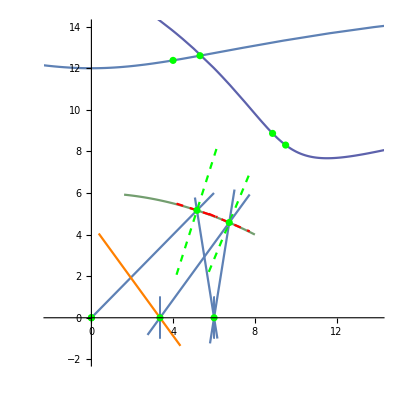

```mathematica
cata = ResourceFunction["CatacausticCurvePlot"][curveparaeqn, {0,0},{t, 0.2, 1,.5}, Axes->True, PlotRange->{{-50, 10},{0,100}}]
orthoorigin = ResourceFunction["Orthotomic"][curveparaeqn, t]
orthodiff = ResourceFunction["Orthotomic"][curveparaeqn, {6.003831069285709,0},t]
orthoplot = ParametricPlot[orthoorigin , {t, -2, 12}];
orthoplot2 = ParametricPlot[orthodiff , {t, -2,12}, ColorFunction->"Rainbow"];
Show[orthoplot,orthoplot2, sourceline, curve, a1tanplot,a1norplot,a1refplot,a2norplot, a2refplot, a3tanplot,a3norplot,a3refplot,a4norplot,a4refplot, ptplot, PlotRange->{{-2, 14},{-2,14}}, AxesOrigin->{0, 0}, PlotLegends->"Expressions"]
```

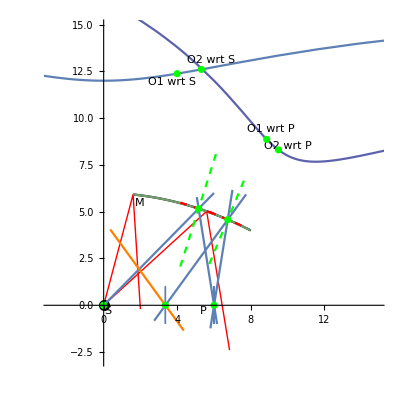

The graphs of the orthotomics O1 and O2 wrt S and P respectively intersect at Point I.